```mathematica
Series[Log[1+x],{x,0,3}]
```

x-x^2/2+x^3/3+O[x]^4

```mathematica
∫_0^∞ ⅇ^(-(j ϵ)/(k T))√ϵ ⅆϵ
```

ConditionalExpression[(√π)/(2 (j/(k T))^(3/2)), Re[j/(k T)]>0]

```mathematica
x=(6.626 10^-34 10^13)/(1.381 10^-23 298.15)
```

1.60925

```mathematica
πf[j_]:=ⅇ^(-x j)(1-ⅇ^-x)
```

```mathematica
πf[0]
πf[1]
πf[2]
πf[3]
πf[4]
```

0.799962

0.160023

0.0320106

0.00640335

0.00128091

```mathematica
1-πf[0]
```

0.200038

```mathematica
α=((1.05457 10^-34)^2)/(2 10^-47 1.381 10^-23 298.15)
```

0.135049

```mathematica
Z=∑_(j=0)^∞ (2j+1)ⅇ^(-α j(j+1))
NZ=N@Z
```

∑_(j=0)^∞ ⅇ^(-0.135049 j (1+j)) (1+2 j)

7.74728

```mathematica
πf2[j_]:=((2j+1)ⅇ^(-α j(j+1)))/NZ
```

```mathematica
πf2[0]
πf2[1]
πf2[2]
πf2[3]
πf2[4]
πf2[5]
πf2[6]
πf2[7]
```

0.129078

0.295576

0.287021

0.178704

0.0779956

0.0247007

0.00577358

0.00100572

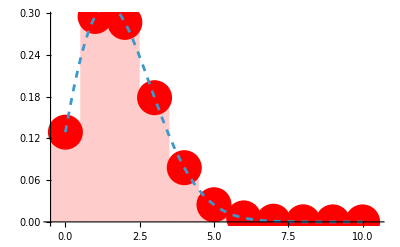

```mathematica
DP=DiscretePlot[πf2[i],{i,0,10},PlotStyle->Red,PlotMarkers->Style["•", FontSize -> 36],ExtentSize->Full];
P=Plot[πf2[i],{i,0,10},PlotStyle->Dashed];
Show[DP,P]
```

```mathematica
Export["C:\\Users\\sfons\\OneDrive\\Escritorio\\MAGISTER\\Física Estadística\\Tarea 2\\grafico414.png",%96,"PNG"]
```

C:\Users\sfons\OneDrive\Escritorio\MAGISTER\Física Estadística\Tarea 2\grafico414.png

```mathematica
Series[De(1-ⅇ^(-β(r-re)))^2,{r,re,3}]
```

De β^2 (r-re)^2-De β^3 (r-re)^3+O[r-re]^4

```mathematica
Z623=∑_(n=0)^∞ ⅇ^(-(n+1/2)u) ⅇ^(χ(n+1/2)^2 u)
```

∑_(n=0)^∞ ⅇ^((-1/2-n) u+(1/2+n)^2 u χ)

```mathematica
Series[Z623,{χ,0,1}]
Z623aprox=%//Normal//FullSimplify
Z623har=(%/.{χ->0})//FullSimplify
```

∑_(n=0)^∞ (ⅇ^((-1/2-n) u)+1/4 ⅇ^(-((1/2+n) u)) (1+2 n)^2 u χ+O[χ]^2)

1/16 (-4+3 u χ+(4+u χ) Cosh[u]) Csch[u/2]^3

1/2 Csch[u/2]

```mathematica
Z623aprox-Z623har//FullSimplify
```

1/16 u χ (3+Cosh[u]) Csch[u/2]^3

```mathematica
Series[Log[A+χ B],{χ,0,1}]
```

Log[A]+(B χ)/A+O[χ]^2

```mathematica
(k T^2  D[(χ u (3+Cosh[u])/(8 Sinh[u/2]^2)/.{u->μ/T}), T]/.{μ->u T})//FullSimplify
```

-(k T u χ (3+Cosh[u]-4 u Coth[u/2]))/(4 (-1+Cosh[u]))

```mathematica
(D[(k T^2  D[(χ u (3+Cosh[u])/(8 Sinh[u/2]^2)/.{u->μ/T}), T]), T]/.{μ->u T})//FullSimplify
```

1/4 k u^2 χ Csch[u/2]^4 (u (2+Cosh[u])-2 Sinh[u])